```mathematica
SetDirectory["/Users/questmac/Public/learning/ml/clojure/mljalfa/resources/aug18"]
```

/Users/questmac/Public/learning/ml/clojure/mljalfa/resources/aug18

```mathematica
data = Association /@ Import["complete.json"];
tDuration = Map[List[#["seoduration"],#["revenue"]]&, data];
tdYears = Partition[tDuration,12];
allYearsFun = Fit[tDuration,{1,x,x^2},x];
partialYearsFun = Map[Fit[#, {1,x},x]&,tdYears];
peryear=Show[ListPlot[tdYears], Plot[partialYearsFun,{x,0,1200000}], ImageSize-> Large];
allyear=Show[ListPlot[tDuration],Plot[allYearsFun,{x,0,1200000}], ImageSize-> Large];
peryear;
```

```mathematica
threeD = Map[Values[KeyTake[#,{"seo","totalduration","revenue"}]]&,data];
solD = NonlinearModelFit[threeD,z =k + a* x *y,{k,a},{x,y}];
```

```mathematica
Show[Plot3D[solD[x,y], {x,0,500000},{y,0,500000}, ImageSize->Large],ListPointPlot3D[threeD]];
```

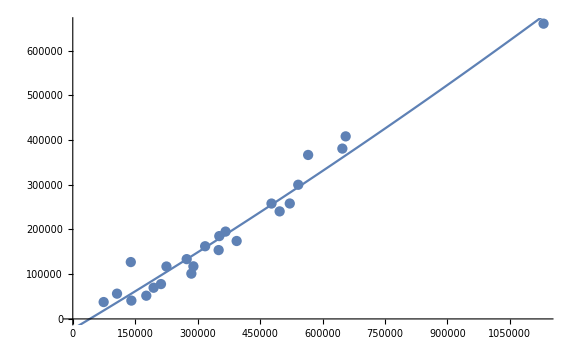

```mathematica
data = Association /@ Import["complete.json"];
seodur = Drop[data,12];
totdur = Drop[data,12];
seodur = Map[{#["seoduration"],#["revenue"]}&, seodur];
totdur = Map[{#["totalduration"],#["revenue"]}&,totdur];
partSeodur = Partition[seodur,12];
partTotdur = Partition[totdur,12];
fSeodur = Fit[seodur,{1,x,x^2},x];
fTotdur = Fit[totdur,{1,x,x^2},x];
pfSeodur = Map[Fit[#,{1,x,x^2},x]&,partSeodur];
pfTotdur =Map[Fit[#,{1,x,x^2},x]&,partTotdur];
allyearSeo =Show[ListPlot[seodur],Plot[fSeodur, {x,0,1600000}],ImageSize-> Large];
partyearSeo = Show[ListPlot[partSeodur], Plot[pfSeodur, {x,0,1600000}], ImageSize -> Large];
allyearTot = Show[ListPlot[totdur],Plot[fTotdur,{x,0,1600000}]];
partyearTot = Show[ListPlot[partTotdur], Plot[pfTotdur,{x,0,1600000}]];
Show[allyearTot,ImageSize-> Large]
```

```mathematica
Map[#[[2]]&,Take[Drop[Import["seodur15.csv"],11],12]];
```